```mathematica
SetDirectory["C:\\Development\\physics\\particle_physics\\capstone_eigenvalue_eigenvector_identity_neutrino_mass_mixing"];
$PrePrint=#/. {Csc[z_]:>1/Defer@Sin[z],Sec[z_]:>1/Defer@Cos[z]}&;
$Assumptions=0<θ12 <Pi/2 && 0<θ23 <Pi/2 && 0< θ13 <Pi/2 && α ∈ Reals && a ∈ Reals && 0<δCP <2Pi && l>0;
```

## Setting parameter values

```mathematica
En=0.001;
a=(2*En*10^9*10^-14)/(2.5*10^-3);
l=1000;
θ13=4.4*Pi/180;
 θ12=33.2*Pi/180;
θ23=46.1*Pi/180;
α=(7.55*10^-5)/(2.5*10^-3);
Δ=(1.267*(2.5*10^-3)*l)/En ;
δCP=1.32*Pi;
```

## Computing Probabilities

```mathematica
O23 = {{1, 0, 0}, {0, Cos[θ23], Sin[θ23]}, {0, -Sin[θ23], Cos[θ23]}};
Udelta = DiagonalMatrix[{1, 1, Exp[I * δCP]}];
O12 = {{Cos[θ12], Sin[θ12], 0}, {-Sin[θ12], Cos[θ12], 0}, {0, 0, 1}};
O13 = {{Cos[θ13], 0, Sin[θ13]}, {0, 1, 0}, {-Sin[θ13], 0, Cos[θ13]}};

M = O13.O12.DiagonalMatrix[{0, α, 1}].Transpose[O12].Transpose[O13] + DiagonalMatrix[{a, 0, 0}];
```

```mathematica
E1=Reverse[Eigenvalues[M]][[1]];
E2=Reverse[Eigenvalues[M]][[2]];
E3=Reverse[Eigenvalues[M]][[3]];

v1=Reverse[Eigenvectors[M]][[1]];
v2=Reverse[Eigenvectors[M]][[2]];
v3=Reverse[Eigenvectors[M]][[3]];
```

```mathematica
eigmat = Expand[Refine[O23.Udelta.Transpose[{v1, v2, v3}]]];
Sdiag = DiagonalMatrix[{Exp[-I * E1 * 2Δ ], Exp[-I * E2* 2Δ ], Exp[-I * E3 * 2Δ ]}];

eigmat // MatrixForm
S = eigmat.Sdiag;
S =S.ConjugateTranspose[eigmat];
P[i_, j_]:=S[[j, i]] * Conjugate[S[[j, i]]]
```

(0.834232+0. ⅈ | 0.54605+0. ⅈ | 0.0767196+0. ⅈ
-0.354968+0.0390527 ⅈ | 0.59639+0.0255621 ⅈ | -0.384953-0.606588 ⅈ
0.41847+0.0375813 ⅈ | -0.587273+0.024599 ⅈ | -0.370448-0.583733 ⅈ)

```mathematica
Pmumu=FullSimplify[ExpToTrig[Refine[P[2, 2]]]]
```

0.434386+0. ⅈ

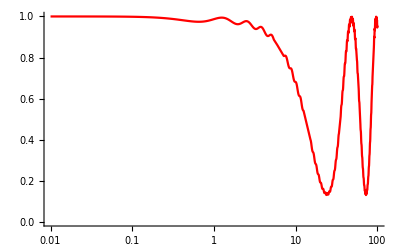

```mathematica
LogLinearPlot[Pee, {l, 10^-2, 10^2}, PlotStyle->{Red}, PlotRange->{0, 1}]
```

## The Hamiltonian

```mathematica
H=Expand[Refine[O23.Udelta.M.ConjugateTranspose[Udelta].Transpose[O23]]];
```

```mathematica
Submatrix[M_, i_, j_]:=Drop[Transpose[Drop[Transpose[M],{i}]],{j}];
EigSubmatrix2by2[M_]:={(M[[1, 1]] + M[[2, 2]] +Sqrt[(M[[1, 1]] - M[[2, 2]] )^2+4*M[[1, 2]] * M[[2, 1]]])/2,(M[[1, 1]] + M[[2, 2]] -Sqrt[(M[[1, 1]] - M[[2, 2]] )^2+4*M[[1, 2]] * M[[2, 1]]])/2};
```

```mathematica
He = Submatrix[H, 1, 1];
Hmu = Submatrix[H, 2, 2];
```

```mathematica
Xie = EigSubmatrix2by2[He][[1]];
Chie = EigSubmatrix2by2[He][[2]];
```

```mathematica
Ximu = EigSubmatrix2by2[Hmu][[1]];
Chimu = EigSubmatrix2by2[Hmu][[2]];
```

```mathematica
quadraticproduct[i_,alpha_,beta_]:=
Module[{lda, adj, product},
lda={E1, E2, E3};

indices = Range[1, 3];
indices = Delete[indices, Position[indices, i]];

adj=Adjugate[lda[[i]]*IdentityMatrix[3]-H][[alpha, beta]];
denom=Product[lda[[i]]-lda[[k]], {k, indices}];
product=adj/denom;

Return[product];
]
PMNSmattermodsq[alpha_, i_]:=
Module[{lda, subeigs},
lda={E1, E2, E3}; (* Should actually be 2E times each eval but it cancels out in the identity so doesn't matter *);
subeigs={{Xie, Chie}, {Ximu, Chimu}}; (* same here *);

indices = Range[1, 3];
indices = Delete[indices, Position[indices, i]];

sublda=subeigs[[alpha]];

num=Product[lda[[i]]-sublda[[j]], {j, Length[sublda]}];
denom=Product[lda[[i]]-lda[[k]], {k, indices}];
modsq=num/denom;

Return[modsq];
]
```

```mathematica
(*In essence, Sin[(lda2-lda1)l/(4En)]^2] becomes Sin[(E2-E1)*2En*l/(4En)]^2] which finally becomes Sin[(E2-E1)l/2]^2]*)
```

```mathematica
deltamsqmat={{1, 1, 1}, {Sin[(E2-E1)Δ]^2, 1, 1}, {Sin[(E3-E1)Δ]^2, Sin[(E3-E2)Δ]^2, 1}};

deltamsqmatdouble={{1, 1, 1}, {Sin[(E2-E1)2Δ]^2, 1, 1}, {Sin[(E3-E1)2Δ]^2,Sin[(E3-E2)2Δ]^2, 1}};
```

```mathematica
Pdisappearance[i_, i_]:=1-4*Sum[ Boole[k>j]*PMNSmattermodsq[i,k]*PMNSmattermodsq[i,j]*deltamsqmat[[k, j]],{k,1,3},{j,1,3}];

Pappearance[a_, b_]:=KroneckerDelta[a, b]-4*Sum[Boole[k>j]*Re[quadraticproduct[k, b, a]*quadraticproduct[j, a, b]]*deltamsqmat[[k, j]], {k, 1, 3}, {j, 1, 3}]+2*Sum[Boole[k>j]*Im[quadraticproduct[k, b, a]*quadraticproduct[j, a, b]]*deltamsqmatdouble[[k, j]], {k, 1, 3}, {j, 1, 3}];
```

```mathematica
Pee=Pdisappearance[1, 1]
```

0.970406-5.69349×10^-17 ⅈ

## Cayley-Hamilton formalism to calculate oscillation probabilities

```mathematica
expansionorder=5;
```

### FIRST TERM

```mathematica
firstdiff12 = truncate[Normal[Series[1/(E1 - E2), {α, 0, expansionorder}, {s13, 0, expansionorder}]], expansionorder];
firstdiff13 = truncate[Normal[Series[1/(E1 - E3), {α, 0, expansionorder}, {s13, 0, expansionorder}]], expansionorder];
firstdiffprod = truncate[firstdiff12* firstdiff13, expansionorder];
firstexpTerm = truncate[Normal[Series[Exp[-I * E1 * l ], {α, 0, expansionorder}, {s13, 0, expansionorder}]], expansionorder];
firstterm = truncate[truncate[firstdiffprod * firstexpTerm, expansionorder]*(truncate[(E2 * E3)*IdentityMatrix[3], expansionorder] - truncate[(E2 + E3) * H, expansionorder] + truncate[H.H, expansionorder]), expansionorder];
```

### SECOND TERM

```mathematica
seconddiff21 = truncate[Normal[Series[1/(E2 -E1), {α, 0, expansionorder}, {s13, 0, expansionorder}]], expansionorder];
seconddiff23 = truncate[Normal[Series[1/(E2 - E3), {α, 0, expansionorder}, {s13, 0, expansionorder}]], expansionorder];
seconddiffprod = truncate[seconddiff21 *seconddiff23, expansionorder];
secondexpTerm = truncate[Normal[Series[Exp[-I * E2 * l ], {α, 0, expansionorder}, {s13, 0, expansionorder}]], expansionorder];
secondterm =truncate[truncate[seconddiffprod * secondexpTerm, expansionorder]*(truncate[(E1 * E3)*IdentityMatrix[3], expansionorder] - truncate[(E1 + E3) * H, expansionorder] + truncate[H.H, expansionorder]), expansionorder];
```

### THIRD TERM

```mathematica
thirddiff31 = truncate[Normal[Series[1/(E3 -E1), {α, 0, expansionorder}, {s13, 0, expansionorder}]], expansionorder];
thirddiff32 = truncate[Normal[Series[1/(E3 - E2), {α, 0, expansionorder}, {s13, 0, expansionorder}]], expansionorder];
thirddiffprod = truncate[thirddiff31 *thirddiff32, expansionorder];
thirdexpTerm = truncate[Normal[Series[Exp[-I * E3 * l ], {α, 0, expansionorder}, {s13, 0, expansionorder}]], expansionorder];
thirdterm =truncate[truncate[thirddiffprod * thirdexpTerm, expansionorder]*(truncate[(E1 * E2)*IdentityMatrix[3], expansionorder] - truncate[(E1 + E2) * H, expansionorder] + truncate[H.H, expansionorder]), expansionorder];
```

### EVOLUTION MATRIX

```mathematica
S=firstterm + secondterm + thirdterm;
S = S /. {l -> 2Δ};
P[i_, j_]:=S[[j, i]] * Conjugate[S[[j, i]]]
```

```mathematica
PeeCayley = truncate[ComplexExpand[Refine[P[1,1]]], 4]
```

```mathematica
C0=truncate[PeeCayley, 0];
C1=truncate[PeeCayley, 1];
C2=truncate[PeeCayley, 2];
C3=truncate[PeeCayley, 3];
C4=truncate[PeeCayley,4];

C0=FullSimplify[C0];

C1alpha=FullSimplify[Coefficient[C1-C0, α]];
C1s13=FullSimplify[Coefficient[C1-C0, s13]];

C2alphasq=FullSimplify[Coefficient[C2-C1-C0, α^2]];
C2alphas13=FullSimplify[Coefficient[C2-C1-C0, α*s13]];
C2s13sq=FullSimplify[Coefficient[C2-C1-C0, s13^2]];

C3alphacub=FullSimplify[Coefficient[C3-C2-C1-C0, α^3]];
C3alphasqs13=FullSimplify[Coefficient[C3-C2-C1-C0, α^2*s13]];
C3alphas13sq=FullSimplify[Coefficient[C3-C2-C1-C0, α*s13^2]];
C3s13cub=FullSimplify[Coefficient[C3-C2-C1-C0, s13^3]];

C4alphaquart=FullSimplify[Coefficient[C4-C3-C2-C1-C0, α^4]];
C4alphacubs13=FullSimplify[Coefficient[C4-C3-C2-C1-C0, α^3*s13]];
C4alphasqs13sq=FullSimplify[Coefficient[C4-C3-C2-C1-C0, α^2*s13^2]];
C4alphas13cub=FullSimplify[Coefficient[C4-C3-C2-C1-C0, α*s13^3]];
C4s13quart=FullSimplify[Coefficient[C4-C3-C2-C1-C0, s13^4]];

(*Manual simplifications done below*)
(*C4alphasqs13sq=1/((-1+a)^4 a^3)(-4 Cos[θ12]^2 Sin[a Δ]^2+a (2 (Cos[2 Δ]-Cos[2 (-1+a) Δ]) Cos[θ12]^2+4 (3+5 Cos[2 θ12]) Sin[a Δ]^2)+a^2 (-8+2 Cos[2 (-1+a) Δ] Cos[θ12]^2+Cos[2 a Δ] (9+25 Cos[2 θ12]+4 Δ Cos[θ12]^2 Sin[2 Δ])+2 Δ Sin[2 a Δ]-4 Cos[2 Δ] Cos[θ12]^2 (1+Δ Sin[2 a Δ])-6 Cos[2 θ12] (4+Δ Sin[2 a Δ]))+a^4 (7+Cos[2 a Δ] (-13+3 Cos[2 θ12])+2 Cos[2 (-1+a) Δ] (3+2 Δ^2+(1-2 Δ^2) Cos[2 θ12])+6 Δ Sin[2 a Δ]-Cos[2 θ12] (5+42 Δ Sin[2 a Δ])+2 Δ (5-3 Cos[2 θ12]) Sin[2 Δ-2 a Δ])+a^3 (-5+Cos[2 a Δ] (1-23 Cos[2 θ12])+23 Cos[2 θ12]+Cos[2 (-1+a) Δ] (3-2 Δ^2+(-1+2 Δ^2) Cos[2 θ12])+2 Δ (-3+13 Cos[2 θ12]) Sin[2 a Δ]+2 Cos[θ12]^2 (Cos[2 Δ]-4 Δ Sin[2 Δ-2 a Δ]))+a^5 (-2+Cos[2 a Δ] (11+7 Cos[2 θ12])+Cos[2 (-1+a) Δ] (-9-2 Δ^2+(-7+2 Δ^2) Cos[2 θ12])+2 Δ (-1+15 Cos[2 θ12]) Sin[2 a Δ]-24 Δ Sin[2 Δ-2 a Δ] Sin[θ12]^2)+a^6 (6 (Cos[2 (-1+a) Δ]-Cos[2 a Δ]) Cos[θ12]^2-8 Δ Cos[2 θ12] Sin[2 a Δ]+8 Δ Sin[2 Δ-2 a Δ] Sin[θ12]^2)) Sin[θ12]^2;
C4s13quart=1/((-1+a)^4 a)(2 a^4 (Cos[2 (-1+a) Δ]-Cos[2 a Δ])-2 a (-3+Cos[2 (-1+a) Δ]+2 Cos[2 a Δ])-4 Sin[a Δ]^2+a^2 (6-6 Cos[2 (-1+a) Δ]-8 Δ Sin[2 Δ-2 a Δ])+a^3 (-2-2 Cos[2 (-1+a) Δ]+4 Cos[2 a Δ]+8 Δ Sin[2 Δ-2 a Δ]));*)
```

```mathematica
C4alphasqs13sq
```

1/((-1+a)^4 a^3)(-1+a (6-a (8+(-1+a) a (-5+2 a)))+Cos[2 a Δ]-Cos[2 θ12]+a ((-1+a)^2 Cos[2 Δ]+(-1+a (1+3 a (1+(-2+a) (-1+a) a)-2 (-1+a)^2 a Δ^2)) Cos[2 (-1+a) Δ]+Cos[2 a Δ] (-6+a (9+a-13 a^2+11 a^3-3 a^4)+2 (-1+a) a (-1+a+2 (-2+a) a^2) Δ Sin[2 Δ])-2 (-1+a) a Δ ((-1+a)^2+(-1+a+2 (-2+a) a^2) Cos[2 Δ]) Sin[2 a Δ])+Cos[2 θ12] (a (10-(-3+a) a (-8+5 a)+(-1+a+a^2 (-1+2 Δ^2+(-2+a) a (-1+3 a+2 Δ^2))) Cos[2 (-1+a) Δ])+(-1+a) Cos[2 a Δ] (-1+a (9+a (-16+a (7+(4-3 a) a)))+2 a^2 (-1+a+4 a^2-2 a^3) Δ Sin[2 Δ])-2 (-1+a)^3 a^2 (-3+4 a) Δ Sin[2 a Δ]+(-1+a) a Cos[2 Δ] (-1+a+2 a (1+a (-1+2 (-2+a) a)) Δ Sin[2 a Δ]))) Sin[θ12]^2

```mathematica
PeeCayley=C0+C1alpha*α+C1s13*s13+C2alphasq*α^2+C2alphas13*α*s13+C2s13sq*s13^2+C3alphacub*α^3+C3alphasqs13*α^2*s13+C3alphas13sq*α*s13^2+C3s13cub*s13^3+C4alphaquart*α^4+C4alphacubs13*α^3*s13+C4alphasqs13sq*α^2*s13^2+C4alphas13cub*α*s13^3+C4s13quart*s13^4
```

1+1/((-1+a)^4 a)s13^4 (2 a^4 (Cos[2 (-1+a) Δ]-Cos[2 a Δ])-2 a (-3+Cos[2 (-1+a) Δ]+2 Cos[2 a Δ])-4 Sin[a Δ]^2+a^2 (6-6 Cos[2 (-1+a) Δ]-8 Δ Sin[2 Δ-2 a Δ])+a^3 (-2-2 Cos[2 (-1+a) Δ]+4 Cos[2 a Δ]+8 Δ Sin[2 Δ-2 a Δ]))-(4 s13^2 Sin[Δ-a Δ]^2)/(-1+a)^2-1/((-1+a)^3 a)s13^2 α (a^3 (-4 Cos[2 (-1+a) Δ]+4 Cos[2 a Δ])+8 Sin[a Δ]^2+a^2 (4+8 Cos[2 (-1+a) Δ]-12 Cos[2 a Δ]-4 Δ Sin[2 Δ-2 a Δ])+4 a (-3+3 Cos[2 a Δ]+Δ Sin[2 Δ-2 a Δ])) Sin[θ12]^2+1/((-1+a)^4 a^3)s13^2 α^2 Sin[θ12]^2 (-4 Cos[θ12]^2 Sin[a Δ]^2+a (2 (Cos[2 Δ]-Cos[2 (-1+a) Δ]) Cos[θ12]^2+4 (3+5 Cos[2 θ12]) Sin[a Δ]^2)+a^2 (-8+2 Cos[2 (-1+a) Δ] Cos[θ12]^2+Cos[2 a Δ] (9+25 Cos[2 θ12]+4 Δ Cos[θ12]^2 Sin[2 Δ])+2 Δ Sin[2 a Δ]-4 Cos[2 Δ] Cos[θ12]^2 (1+Δ Sin[2 a Δ])-6 Cos[2 θ12] (4+Δ Sin[2 a Δ]))+a^4 (7+Cos[2 a Δ] (-13+3 Cos[2 θ12])+2 Cos[2 (-1+a) Δ] (3+2 Δ^2+(1-2 Δ^2) Cos[2 θ12])+6 Δ Sin[2 a Δ]-Cos[2 θ12] (5+42 Δ Sin[2 a Δ])+2 Δ (5-3 Cos[2 θ12]) Sin[2 Δ-2 a Δ])+a^3 (-5+Cos[2 a Δ] (1-23 Cos[2 θ12])+23 Cos[2 θ12]+Cos[2 (-1+a) Δ] (3-2 Δ^2+(-1+2 Δ^2) Cos[2 θ12])+2 Δ (-3+13 Cos[2 θ12]) Sin[2 a Δ]+2 Cos[θ12]^2 (Cos[2 Δ]-4 Δ Sin[2 Δ-2 a Δ]))+a^5 (-2+Cos[2 a Δ] (11+7 Cos[2 θ12])+Cos[2 (-1+a) Δ] (-9-2 Δ^2+(-7+2 Δ^2) Cos[2 θ12])+2 Δ (-1+15 Cos[2 θ12]) Sin[2 a Δ]-24 Δ Sin[2 Δ-2 a Δ] Sin[θ12]^2)+a^6 (6 (Cos[2 (-1+a) Δ]-Cos[2 a Δ]) Cos[θ12]^2-8 Δ Cos[2 θ12] Sin[2 a Δ]+8 Δ Sin[2 Δ-2 a Δ] Sin[θ12]^2))-(α^2 Sin[a Δ]^2 Sin[2 θ12]^2)/a^2+(2 α^3 Cos[2 θ12] (-1+a Δ Cot[a Δ]) Sin[a Δ]^2 Sin[2 θ12]^2)/a^3+(α^4 (-2-4 Cos[4 θ12]-2 Cos[2 a Δ] (-1+a^2 Δ^2+(-2+a^2 Δ^2) Cos[4 θ12])+a Δ (3+5 Cos[4 θ12]) Sin[2 a Δ]) Sin[2 θ12]^2)/(4 a^4)

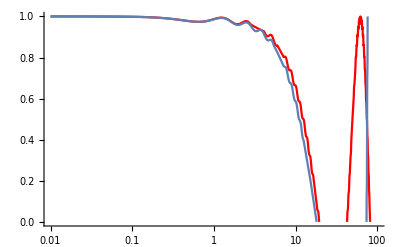

```mathematica
plotPee2ndOrderL=1-(4 Sin[θ13]^2 Sin[(-1+a) Δ]^2)/(-1+a)^2-(α^2 Sin[a Δ]^2 Sin[2 θ12]^2)/a^2/. {a->0.02, θ13->4.4*Pi/180, θ12->33.2*Pi/180,θ23->46.1*Pi/180, α->0.026, Δ->(1.27*(2*10^-3)*l)/0.001 };
plotPee4thOrderL = PeeCayley/. {s13->Sin[θ13]} /. {a->0.02, θ13->4.4*Pi/180, θ12->33.2*Pi/180,θ23->46.1*Pi/180, α->0.026, Δ->(1.27*(2*10^-3)*l)/0.001 };
p3 = LogLinearPlot[plotPee2ndOrderL, {l, 10^-2, 10^2}, PlotStyle->{Red}, PlotRange->{0, 1}];
p4 = LogLinearPlot[plotPee4thOrderL, {l, 10^-2, 10^2}, PlotRange -> {0, 1}];
Show[p3, p4]
```

```mathematica
S21=ComplexExpand[ExpToTrig[Refine[S[[2, 1]]]]]
```

```mathematica
ReS21=ComplexExpand[Re[S21]]
```

```mathematica
denoms=groupbydenominator[ReS21]
```

```mathematica
ReS21=parallelrefinebydenom[ReS21]
```

```mathematica
ImS21=ComplexExpand[Im[S21]]
```

```mathematica
ImS21=parallelrefinebydenom[ImS21]
```

```mathematica
S21=ReS21+I*ImS21
```

```mathematica
PemuCayley = truncate[ComplexExpand[Refine[S21*Conjugate[S21]]], 5]
(* FullSimplify[TrigReduce[truncate[Expand[ComplexExpand[component]*(ComplexExpand[Conjugate[component]])]]]] /. {l -> {2Δ}} *)
```

```mathematica
C0=truncate[PemuCayley, 0];
C1=truncate[PemuCayley, 1];
C2=truncate[PemuCayley, 2];
C3=truncate[PemuCayley, 3];
C4=truncate[PemuCayley, 4];
C5=truncate[PemuCayley, 5];

C0=FullSimplify[C0];

C1alpha=FullSimplify[Coefficient[C1-C0, α]];
C1s13=FullSimplify[Coefficient[C1-C0, s13]];

C2alphasq=FullSimplify[Coefficient[C2-C1-C0, α^2]];
C2alphas13=FullSimplify[Coefficient[C2-C1-C0, α*s13]];
C2s13sq=FullSimplify[Coefficient[C2-C1-C0, s13^2]];


C3alphacub=FullSimplify[Coefficient[C3-C2-C1-C0, α^3]];
C3alphasqs13=FullSimplify[Coefficient[C3-C2-C1-C0, α^2*s13]];
C3alphas13sq=FullSimplify[Coefficient[C3-C2-C1-C0, α*s13^2]];
C3s13cub=FullSimplify[Coefficient[C3-C2-C1-C0, s13^3]];

C4alphaquart=FullSimplify[Coefficient[C4-C3-C2-C1-C0, α^4]];
C4alphacubs13=FullSimplify[Coefficient[C4-C3-C2-C1-C0, α^3*s13]];
C4alphasqs13sq=FullSimplify[Coefficient[C4-C3-C2-C1-C0, α^2*s13^2]];
C4alphas13cub=FullSimplify[Coefficient[C4-C3-C2-C1-C0, α*s13^3]];
C4s13quart=FullSimplify[Coefficient[C4-C3-C2-C1-C0, s13^4]];

C5alphafive=FullSimplify[Coefficient

(*Manual simplifications done below*)
(*C3alphasqs13=1/(4 (-1+a)^2 a^2)(2 (-Cos[2 Δ-δCP]+Cos[2 a Δ-δCP]-Cos[δCP]+Cos[2 (-1+a) Δ+δCP]) Cos[2 θ12]+a (-4 Δ Cos[(-2+a) Δ+δCP] Sin[a Δ]+2 Cos[2 θ12] (Cos[2 Δ-δCP]-Cos[2 a Δ-δCP]+Cos[δCP]-Cos[2 (-1+a) Δ+δCP]+Δ (-Sin[2 Δ-δCP]+2 Sin[2 a Δ-δCP]+Sin[2 (-1+a) Δ+δCP])))+a^2 (4 Δ Cos[θ12]^2 Sin[2 Δ-δCP]-4 Δ Cos[2 θ12] Sin[2 a Δ-δCP]+2 (-Cos[2 Δ-δCP]+Cos[2 a Δ-δCP]-Cos[δCP]+Cos[2 (-1+a) Δ+δCP]+2 Δ Sin[2 (-1+a) Δ+δCP]) Sin[θ12]^2)) Sin[2 θ12] Sin[2 θ23];*)
C4alphacubs13=-1/(16 (-1+a)^3 a^3)(2 Cos[2 (-1+a) Δ+δCP]-Cos[2 a Δ+δCP]+(-8 Cos[δCP]+6 Cos[2 (-1+a) Δ+δCP]+Cos[2 a Δ+δCP]) Cos[4 θ12]-2 Cos[2 Δ-δCP] (1+3 Cos[4 θ12])+Cos[2 a Δ-δCP] (1+7 Cos[4 θ12])+2 a (-2 Cos[2 (-1+a) Δ+δCP]+Cos[2 a Δ+δCP]+Cos[2 Δ-δCP] (2+6 Cos[4 θ12])-Cos[2 a Δ-δCP] (1+7 Cos[4 θ12])-8 Δ Cos[(-2+a) Δ+δCP] Cos[2 θ12] Sin[a Δ]-Δ Sin[2 Δ-δCP]+2 Δ Sin[2 a Δ-δCP]+Δ Sin[2 (-1+a) Δ+δCP]+Cos[4 θ12] (8 Cos[δCP]-6 Cos[2 (-1+a) Δ+δCP]-Cos[2 a Δ+δCP]+3 Δ (-Sin[2 Δ-δCP]+2 Sin[2 a Δ-δCP]+Sin[2 (-1+a) Δ+δCP])))+a^2 (8 Cos[2 Δ-δCP] Cos[θ12]^2 (1+Δ^2+(-2+Δ^2) Cos[2 θ12])-4 Cos[δCP] (Cos[2 θ12]+Cos[4 θ12])+4 Cos[2 a Δ-δCP] (-2 Δ^2+Cos[2 θ12]+(1-2 Δ^2) Cos[4 θ12])+2 Cos[2 (-1+a) Δ+δCP] (-3 Δ^2+(2+4 Δ^2) Cos[2 θ12]-(-2+Δ^2) Cos[4 θ12])+4 Δ (4 Cos[θ12]^2 (-1+3 Cos[2 θ12]) Sin[2 Δ-δCP]-2 (1+3 Cos[4 θ12]) Sin[2 a Δ-δCP]+4 (1+3 Cos[2 θ12]) Sin[2 (-1+a) Δ+δCP] Sin[θ12]^2))+a^4 (Cos[δCP] (-1+Cos[4 θ12])+4 (-4 Δ^2 Cos[2 a Δ-δCP] Cos[2 θ12]^2+Cos[2 Δ-δCP] Cos[θ12]^2 (1+2 Δ^2+(-1+2 Δ^2) Cos[2 θ12])+(Cos[2 (-1+a) Δ+δCP] (-1-2 Δ^2+(-1+2 Δ^2) Cos[2 θ12])-4 Δ Cos[2 θ12] Sin[2 a Δ-δCP]) Sin[θ12]^2+4 Δ Sin[2 (-1+a) Δ+δCP] Sin[θ12]^4)+2 (Cos[2 a Δ+δCP]+2 Δ Sin[2 Δ-δCP]) Sin[2 θ12]^2)+a^3 (-2 Cos[2 Δ-δCP] ((-4+8 Δ^2) Cos[2 θ12]+(1+2 Δ^2) (3+Cos[4 θ12]))+8 (Cos[2 a Δ-δCP] Cos[2 θ12] (-1+(1+4 Δ^2) Cos[2 θ12])-2 Δ Cos[θ12]^2 Cos[2 θ12] Sin[2 Δ-δCP]+Δ (Cos[2 θ12]+Cos[4 θ12]) Sin[2 a Δ-δCP]+Cos[δCP] (1+3 Cos[2 θ12]) Sin[θ12]^2+2 (1+2 Δ^2) Cos[2 (-1+a) Δ+δCP] Sin[θ12]^4)-4 (Cos[2 a Δ+δCP]+2 Δ Sin[2 (-1+a) Δ+δCP]) Sin[2 θ12]^2)) Sin[2 θ12] Sin[2 θ23];
```

```mathematica
Coefficient[C5-C4-C3-C2-C1-C0, α^3*s13^2]
```

0

```mathematica
C4alphacubs13
```

-1/(16 (-1+a)^3 a^3)(2 Cos[2 (-1+a) Δ+δCP]-Cos[2 a Δ+δCP]+Cos[2 a Δ-δCP] (1+2 a (-1+2 a (a-2 (-1+a)^2 Δ^2))+4 (1-2 a) a^2 Cos[2 θ12]+(7+2 a (-7+2 a (1+a-2 (-1+a)^2 Δ^2))) Cos[4 θ12])+Cos[2 Δ-δCP] (-2+a (4+a ((-6+a) a+6 (-1+a)^2 Δ^2))+4 a^2 (-1+2 a+2 (-1+a)^2 Δ^2) Cos[2 θ12]+(-6+a (12+a (-4-a (2+a)+2 (-1+a)^2 Δ^2))) Cos[4 θ12])+a (-a^2 (2+a) Cos[δCP]-(4+a ((-6+a) a+6 (-1+a)^2 Δ^2)) Cos[2 (-1+a) Δ+δCP]+2 Cos[2 a Δ+δCP]-2 a^2 Cos[2 a Δ+δCP]+a^3 Cos[2 a Δ+δCP]-2 Δ Sin[2 Δ-δCP]+4 a Δ Sin[2 Δ-δCP]-4 a^2 Δ Sin[2 Δ-δCP]+2 a^3 Δ Sin[2 Δ-δCP]+4 Δ Sin[2 a Δ-δCP]-8 a Δ Sin[2 a Δ-δCP]+4 a^3 Δ Sin[2 a Δ-δCP]+2 (-1+a) (-1+a+3 a^2) Δ Sin[2 (-1+a) Δ+δCP])+4 a Cos[2 θ12] (a (-1+2 a) Cos[δCP]+a (1-2 a+2 (-1+a)^2 Δ^2) Cos[2 (-1+a) Δ+δCP]+2 (-1+a) Δ (-((-1+a) Sin[2 Δ-δCP])-a^2 Sin[2 a Δ-δCP])-2 (1-2 a+a^3) Δ Sin[2 (-1+a) Δ+δCP])+Cos[4 θ12] ((-8+a (16+a (-4+(-6+a) a))) Cos[δCP]+(6+a (-12+a (4+2 a+a^2-2 (-1+a)^2 Δ^2))) Cos[2 (-1+a) Δ+δCP]+(-1+a) (-(-1+a)^2 (1+a) Cos[2 a Δ+δCP]+2 a (-3+a (3+a)) Δ (-Sin[2 Δ-δCP]+2 Sin[2 a Δ-δCP]+Sin[2 (-1+a) Δ+δCP])))) Sin[2 θ12] Sin[2 θ23]

```mathematica
Collect[Expand[(2 Cos[2 (-1+a) Δ+δCP]-Cos[2 a Δ+δCP]+Cos[2 a Δ-δCP] (1+2 a (-1+2 a (a-2 (-1+a)^2 Δ^2))+4 (1-2 a) a^2 Cos[2 θ12]+(7+2 a (-7+2 a (1+a-2 (-1+a)^2 Δ^2))) Cos[4 θ12])+Cos[2 Δ-δCP] (-2+a (4+a ((-6+a) a+6 (-1+a)^2 Δ^2))+4 a^2 (-1+2 a+2 (-1+a)^2 Δ^2) Cos[2 θ12]+(-6+a (12+a (-4-a (2+a)+2 (-1+a)^2 Δ^2))) Cos[4 θ12])+a (-a^2 (2+a) Cos[δCP]-(4+a ((-6+a) a+6 (-1+a)^2 Δ^2)) Cos[2 (-1+a) Δ+δCP]+2 Cos[2 a Δ+δCP]-2 a^2 Cos[2 a Δ+δCP]+a^3 Cos[2 a Δ+δCP]-2 Δ Sin[2 Δ-δCP]+4 a Δ Sin[2 Δ-δCP]-4 a^2 Δ Sin[2 Δ-δCP]+2 a^3 Δ Sin[2 Δ-δCP]+4 Δ Sin[2 a Δ-δCP]-8 a Δ Sin[2 a Δ-δCP]+4 a^3 Δ Sin[2 a Δ-δCP]+2 (-1+a) (-1+a+3 a^2) Δ Sin[2 (-1+a) Δ+δCP])+4 a Cos[2 θ12] (a (-1+2 a) Cos[δCP]+a (1-2 a+2 (-1+a)^2 Δ^2) Cos[2 (-1+a) Δ+δCP]+2 (-1+a) Δ (-((-1+a) Sin[2 Δ-δCP])-a^2 Sin[2 a Δ-δCP])-2 (1-2 a+a^3) Δ Sin[2 (-1+a) Δ+δCP])+Cos[4 θ12] ((-8+a (16+a (-4+(-6+a) a))) Cos[δCP]+(6+a (-12+a (4+2 a+a^2-2 (-1+a)^2 Δ^2))) Cos[2 (-1+a) Δ+δCP]+(-1+a) (-(-1+a)^2 (1+a) Cos[2 a Δ+δCP]+2 a (-3+a (3+a)) Δ (-Sin[2 Δ-δCP]+2 Sin[2 a Δ-δCP]+Sin[2 (-1+a) Δ+δCP])))) ], a, FullSimplify]
```

2 Cos[2 (-1+a) Δ+δCP]-Cos[2 a Δ+δCP]+(-8 Cos[δCP]+6 Cos[2 (-1+a) Δ+δCP]+Cos[2 a Δ+δCP]) Cos[4 θ12]-2 Cos[2 Δ-δCP] (1+3 Cos[4 θ12])+Cos[2 a Δ-δCP] (1+7 Cos[4 θ12])+2 a (-2 Cos[2 (-1+a) Δ+δCP]+Cos[2 a Δ+δCP]+Cos[2 Δ-δCP] (2+6 Cos[4 θ12])-Cos[2 a Δ-δCP] (1+7 Cos[4 θ12])-8 Δ Cos[(-2+a) Δ+δCP] Cos[2 θ12] Sin[a Δ]-Δ Sin[2 Δ-δCP]+2 Δ Sin[2 a Δ-δCP]+Δ Sin[2 (-1+a) Δ+δCP]+Cos[4 θ12] (8 Cos[δCP]-6 Cos[2 (-1+a) Δ+δCP]-Cos[2 a Δ+δCP]+3 Δ (-Sin[2 Δ-δCP]+2 Sin[2 a Δ-δCP]+Sin[2 (-1+a) Δ+δCP])))+a^2 (8 Cos[2 Δ-δCP] Cos[θ12]^2 (1+Δ^2+(-2+Δ^2) Cos[2 θ12])-4 Cos[δCP] (Cos[2 θ12]+Cos[4 θ12])+4 Cos[2 a Δ-δCP] (-2 Δ^2+Cos[2 θ12]+(1-2 Δ^2) Cos[4 θ12])+2 Cos[2 (-1+a) Δ+δCP] (-3 Δ^2+(2+4 Δ^2) Cos[2 θ12]-(-2+Δ^2) Cos[4 θ12])+4 Δ (4 Cos[θ12]^2 (-1+3 Cos[2 θ12]) Sin[2 Δ-δCP]-2 (1+3 Cos[4 θ12]) Sin[2 a Δ-δCP]+4 (1+3 Cos[2 θ12]) Sin[2 (-1+a) Δ+δCP] Sin[θ12]^2))+a^4 (Cos[δCP] (-1+Cos[4 θ12])+4 (-4 Δ^2 Cos[2 a Δ-δCP] Cos[2 θ12]^2+Cos[2 Δ-δCP] Cos[θ12]^2 (1+2 Δ^2+(-1+2 Δ^2) Cos[2 θ12])+(Cos[2 (-1+a) Δ+δCP] (-1-2 Δ^2+(-1+2 Δ^2) Cos[2 θ12])-4 Δ Cos[2 θ12] Sin[2 a Δ-δCP]) Sin[θ12]^2+4 Δ Sin[2 (-1+a) Δ+δCP] Sin[θ12]^4)+2 (Cos[2 a Δ+δCP]+2 Δ Sin[2 Δ-δCP]) Sin[2 θ12]^2)+a^3 (-2 Cos[2 Δ-δCP] ((-4+8 Δ^2) Cos[2 θ12]+(1+2 Δ^2) (3+Cos[4 θ12]))+8 (Cos[2 a Δ-δCP] Cos[2 θ12] (-1+(1+4 Δ^2) Cos[2 θ12])-2 Δ Cos[θ12]^2 Cos[2 θ12] Sin[2 Δ-δCP]+Δ (Cos[2 θ12]+Cos[4 θ12]) Sin[2 a Δ-δCP]+Cos[δCP] (1+3 Cos[2 θ12]) Sin[θ12]^2+2 (1+2 Δ^2) Cos[2 (-1+a) Δ+δCP] Sin[θ12]^4)-4 (Cos[2 a Δ+δCP]+2 Δ Sin[2 (-1+a) Δ+δCP]) Sin[2 θ12]^2)

```mathematica
PemuCayley=C0+C1alpha*α+C1s13*s13+C2alphasq*α^2+C2alphas13*α*s13+C2s13sq*s13^2+C3alphacub*α^3+C3alphasqs13*α^2*s13+C3alphas13sq*α*s13^2+C3s13cub*s13^3
```

(α^2 Cos[θ23]^2 Sin[a Δ]^2 Sin[2 θ12]^2)/a^2-(2 α^3 Cos[2 θ12] Cos[θ23]^2 (-1+a Δ Cot[a Δ]) Sin[a Δ]^2 Sin[2 θ12]^2)/a^3+(4 s13^2 Sin[Δ-a Δ]^2 Sin[θ23]^2)/(-1+a)^2-(8 s13^2 α Sin[Δ-a Δ] ((-1+a) Δ Cos[Δ-a Δ]+a Sin[Δ-a Δ]) Sin[θ12]^2 Sin[θ23]^2)/(-1+a)^3-(2 s13 α Cos[Δ-δCP] Sin[a Δ] Sin[Δ-a Δ] Sin[2 θ12] Sin[2 θ23])/((-1+a) a)+1/(4 (-1+a)^2 a^2)s13 α^2 (2 (-Cos[2 Δ-δCP]+Cos[2 a Δ-δCP]-Cos[δCP]+Cos[2 (-1+a) Δ+δCP]) Cos[2 θ12]+a (-4 Δ Cos[(-2+a) Δ+δCP] Sin[a Δ]+2 Cos[2 θ12] (Cos[2 Δ-δCP]-Cos[2 a Δ-δCP]+Cos[δCP]-Cos[2 (-1+a) Δ+δCP]+Δ (-Sin[2 Δ-δCP]+2 Sin[2 a Δ-δCP]+Sin[2 (-1+a) Δ+δCP])))+a^2 (4 Δ Cos[θ12]^2 Sin[2 Δ-δCP]-4 Δ Cos[2 θ12] Sin[2 a Δ-δCP]+2 (-Cos[2 Δ-δCP]+Cos[2 a Δ-δCP]-Cos[δCP]+Cos[2 (-1+a) Δ+δCP]+2 Δ Sin[2 (-1+a) Δ+δCP]) Sin[θ12]^2)) Sin[2 θ12] Sin[2 θ23]

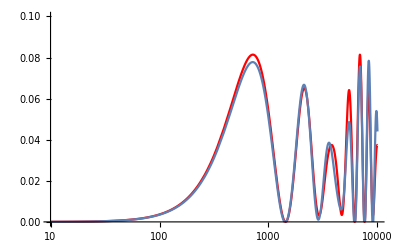

```mathematica
plotPemu2ndOrderL=((α^2 Cos[θ23]^2 Sin[a Δ]^2 Sin[2 θ12]^2)/a^2+(4 Sin[θ13]^2 Sin[Δ-a Δ]^2 Sin[θ23]^2)/(-1+a)^2-(2 Sin[θ13] α Cos[Δ-δCP] Sin[a Δ] Sin[Δ-a Δ] Sin[2 θ12] Sin[2 θ23])/((-1+a) a))/. {a->0.2, θ13->Pi/20, θ12->Pi/6,θ23->Pi/4,δCP->Pi/6, α->0.03, Δ->(1.27*(2*10^-3)*l)/1 };
plotPemu5thOrderL = PemuCayley /. {s13->Sin[θ13]} /. {a->0.2, θ13->Pi/20, θ12->Pi/6,θ23->Pi/4,δCP->Pi/6, α->0.03, Δ->(1.27*(2*10^-3)*l)/1 };

p3 = LogLinearPlot[plotPemu2ndOrderL, {l, 10, 10^4}, PlotStyle->{Red}, PlotRange->{0, 0.1}];
p4 = LogLinearPlot[plotPemu5thOrderL, {l, 10, 10^4}, PlotRange -> {0, 0.1}];
Show[p3, p4]
```

```mathematica
PmumuCayley = Expand[ExpToTrig[truncate[ComplexExpand[Refine[P[2, 2]]]]]]
```

```mathematica
C0 = FullSimplify[Expand[PmumuCayley /. {α->0, s13->0} /. {α^2 -> 0, s13 *α -> 0, s13^2 -> 0}]];
C1 = FullSimplify[Expand[PmumuCayley - C0 /. {s13->0}/. {α^2 -> 0, s13 *α -> 0, s13^2 -> 0}]];
C2 = FullSimplify[Expand[PmumuCayley -C0 /. {α->0}/. {α^2 -> 0, s13 *α -> 0, s13^2 -> 0}]];
C3 = FullSimplify[Expand[PmumuCayley -C0 -C1-C2/. {s13 *α -> 0, s13^2 -> 0}]];
C4 = FullSimplify[Expand[PmumuCayley -C0 -C1-C2/. {α^2 ->0, s13^2 -> 0}]];
C5 = FullSimplify[Expand[PmumuCayley -C0 -C1-C2/. {α^2 ->0, s13 *α -> 0}]];
```

```mathematica
Simplify[1/4 (3+Cos[2 Δ]+2 Cos[4 θ23] Sin[Δ]^2)-(1-(Sin[2 θ23 ] * Sin[Δ])^2)]
Simplify[α Δ Cos[θ12]^2 Sin[2 Δ] Sin[2 θ23]^2 - (α Cos[θ12]^2 Sin[2 θ23]^2 Δ Sin[2Δ])]
Simplify[1/(8 a^2)α^2 Cos[θ12]^2 Cos[θ23]^2 (Cos[2 Δ-2 θ12]-2 Cos[2 a Δ-2 θ12]+Cos[2 (Δ+θ12)]-2 (2+Cos[2 ((-1+a) Δ+θ12)]+Cos[2 (Δ-a Δ+θ12)]+Cos[2 (a Δ+θ12)])+2 Cos[2 θ12] (2+Cos[2 Δ] (1-4 a^2 Δ^2+(-2+4 a^2 Δ^2) Cos[2 θ23]))+Cos[2 (-1+a) Δ] (4-8 Cos[2 θ23] Sin[θ12]^2)+Cos[2 a Δ] (4+8 Cos[2 θ23] Sin[θ12]^2)-8 (1+2 a^2 Δ^2) Cos[2 Δ] Sin[θ23]^2-8 Sin[θ12]^2 (Cos[2 θ23]+8 a Δ Cos[Δ] Sin[Δ] Sin[θ23]^2)) - (-α^2 Sin[2θ12]^2 Cos[θ23]^2 Sin[a Δ]^2/a^2 - α^2 Cos[θ12]^4 Sin[2 θ23]^2 Δ^2 Cos[2Δ]+1/(2a)α^2 Sin[2θ12]^2 Sin[2 θ23]^2(Sin[Δ] Sin[a Δ]/a Cos[(a - 1)Δ] - Δ/2 Sin[2Δ]))]
Simplify[(s13 α Cos[δCP] Sin[2 θ12] (-1+Cos[2 a Δ]+(-1+2 a^2+Cos[2 a Δ]) Cos[2 θ23]+Cos[2 Δ] (-1+(1-2 a^2) Cos[2 θ23])+2 Cos[2 (-1+a) Δ] Sin[θ23]^2) Sin[2 θ23])/(2 (-1+a) a)-(-2α s13 Sin[2θ12] Sin[2 θ23]Cos[δCP]Cos[Δ] Sin[a Δ]/a Sin[(a-1)Δ]/(a - 1)+2/(a-1)α s13 Sin[2 θ12]Sin[2 θ23]Cos[2 θ23]Cos[δCP]Sin[Δ](a Sin[Δ]-Sin[a Δ]/a Cos[(a-1)Δ]))]
Simplify[(2 s13^2 Sin[θ23]^2 (Cos[θ23]^2 (-Cos[2 Δ]+Cos[2 a Δ]+2 (-1+a) a Δ Sin[2 Δ])-2 Sin[(-1+a) Δ]^2 Sin[θ23]^2))/(-1+a)^2-(-4 s13^2 Sin[θ23]^2 Sin[(a-1)Δ]^2/(a-1)^2-2/(a-1)s13^2 Sin[2θ23]^2(Sin[Δ]Cos[a Δ] Sin[(a-1)Δ]/(a-1)-a/2 Δ Sin[2Δ]))]
```

0

0

0

«2 more identical outputs»

```mathematica
PmumuCayleySimplified = C0 + C1 + C2 + C3 + C4 + C5
```

1/4 (3+Cos[2 Δ]+2 Cos[4 θ23] Sin[Δ]^2)+(2 s13^2 Sin[θ23]^2 (Cos[θ23]^2 (-Cos[2 Δ]+Cos[2 a Δ]+2 (-1+a) a Δ Sin[2 Δ])-2 Sin[(-1+a) Δ]^2 Sin[θ23]^2))/(-1+a)^2+1/(8 a^2)α^2 Cos[θ12]^2 Cos[θ23]^2 (Cos[2 Δ-2 θ12]-2 Cos[2 a Δ-2 θ12]+Cos[2 (Δ+θ12)]-2 (2+Cos[2 ((-1+a) Δ+θ12)]+Cos[2 (Δ-a Δ+θ12)]+Cos[2 (a Δ+θ12)])+2 Cos[2 θ12] (2+Cos[2 Δ] (1-4 a^2 Δ^2+(-2+4 a^2 Δ^2) Cos[2 θ23]))+Cos[2 (-1+a) Δ] (4-8 Cos[2 θ23] Sin[θ12]^2)+Cos[2 a Δ] (4+8 Cos[2 θ23] Sin[θ12]^2)-8 (1+2 a^2 Δ^2) Cos[2 Δ] Sin[θ23]^2-8 Sin[θ12]^2 (Cos[2 θ23]+8 a Δ Cos[Δ] Sin[Δ] Sin[θ23]^2))+(s13 α Cos[δCP] Sin[2 θ12] (-1+Cos[2 a Δ]+(-1+2 a^2+Cos[2 a Δ]) Cos[2 θ23]+Cos[2 Δ] (-1+(1-2 a^2) Cos[2 θ23])+2 Cos[2 (-1+a) Δ] Sin[θ23]^2) Sin[2 θ23])/(2 (-1+a) a)+α Δ Cos[θ12]^2 Sin[2 Δ] Sin[2 θ23]^2

## Eigenvector perturbations to compute oscillation probabilities

```mathematica
eigmat = Expand[Refine[O23.Udelta.Transpose[{v1, v2, v3}]]];
Sdiag = truncate[Normal[Series[DiagonalMatrix[{Exp[-I * E1 * 2Δ ], Exp[-I * E2* 2Δ ], Exp[-I * E3 * 2Δ ]}], {α, 0, 2}, {s13, 0, 2}]]];
```

```mathematica
S2 = truncate[ComplexExpand[eigmat.Sdiag]];
S2 = truncate[ComplexExpand[S2.ConjugateTranspose[eigmat]]];
P2[i_, j_]:=S2[[j, i]] * Conjugate[S2[[j, i]]]
```

```mathematica
Pee= Expand[ExpToTrig[truncate[ComplexExpand[Refine[P2[1, 1]]]]]]
```

(2 s13^2 Cos[2 Δ] Cos[2 a Δ])/(-1+a)^4-(4 a s13^2 Cos[2 Δ] Cos[2 a Δ])/(-1+a)^4+(2 a^2 s13^2 Cos[2 Δ] Cos[2 a Δ])/(-1+a)^4+Cos[2 a Δ]^2-(2 s13^2 Cos[2 a Δ]^2)/(-1+a)^2+(2 s13^2 Sin[2 Δ] Sin[2 a Δ])/(-1+a)^4-(4 a s13^2 Sin[2 Δ] Sin[2 a Δ])/(-1+a)^4+(2 a^2 s13^2 Sin[2 Δ] Sin[2 a Δ])/(-1+a)^4+Sin[2 a Δ]^2-(2 s13^2 Sin[2 a Δ]^2)/(-1+a)^2+(α^2 Cos[2 a Δ] Sin[2 θ12]^2)/(2 a^2)-(α^2 Cos[2 a Δ]^2 Sin[2 θ12]^2)/(2 a^2)-(α^2 Sin[2 a Δ]^2 Sin[2 θ12]^2)/(2 a^2)

```mathematica
C0 = FullSimplify[Expand[Pee /. {α->0, s13->0} /. {α^2 -> 0, s13 *α -> 0, s13^2 -> 0}]];
C1 = FullSimplify[Expand[Pee - C0 /. {s13->0}/. {α^2 -> 0, s13 *α -> 0, s13^2 -> 0}]];
C2 = FullSimplify[Expand[Pee -C0 /. {α->0}/. {α^2 -> 0, s13 *α -> 0, s13^2 -> 0}]];
C3 = FullSimplify[Expand[Pee -C0 -C1-C2/. {s13 *α -> 0, s13^2 -> 0}]];
C4 = FullSimplify[Expand[Pee -C0 -C1-C2/. {α^2 ->0, s13^2 -> 0}]];
C5 = FullSimplify[Expand[Pee -C0 -C1-C2/. {α^2 ->0, s13 *α -> 0}]];
```

```mathematica
PeeSimplified = C0 + C1 + C2 + C3 + C4 + C5
```

```mathematica
Pemu= Expand[ExpToTrig[truncate[ComplexExpand[Refine[P2[1, 2]]]]]];
```

```mathematica
C0 = FullSimplify[Expand[Pemu /. {α->0, s13->0} /. {α^2 -> 0, s13 *α -> 0, s13^2 -> 0}]];
C1 = FullSimplify[Expand[Pemu - C0 /. {s13->0}/. {α^2 -> 0, s13 *α -> 0, s13^2 -> 0}]];
C2 = FullSimplify[Expand[Pemu -C0 /. {α->0}/. {α^2 -> 0, s13 *α -> 0, s13^2 -> 0}]];
C3 = FullSimplify[Expand[Pemu -C0 -C1-C2/. {s13 *α -> 0, s13^2 -> 0}]];
C4 = FullSimplify[Expand[Pemu -C0 -C1-C2/. {α^2 ->0, s13^2 -> 0}]];
C5 = FullSimplify[Expand[Pemu -C0 -C1-C2/. {α^2 ->0, s13 *α -> 0}]];
```

```mathematica
PemuSimplified = C0 + C1 + C2 + C3 + C4 + C5
```

(α^2 Cos[θ23]^2 Sin[a Δ]^2 Sin[2 θ12]^2)/a^2+(4 s13^2 Sin[Δ-a Δ]^2 Sin[θ23]^2)/(-1+a)^2-(2 s13 α Cos[Δ-δCP] Sin[a Δ] Sin[Δ-a Δ] Sin[2 θ12] Sin[2 θ23])/((-1+a) a)

```mathematica
Pmumu = Expand[ExpToTrig[truncate[ComplexExpand[Refine[P2[2, 2]]]]]];
```

```mathematica
C0 = FullSimplify[Expand[Pmumu /. {α->0, s13->0} /. {α^2 -> 0, s13 *α -> 0, s13^2 -> 0}]];
C1 = FullSimplify[Expand[Pmumu - C0 /. {s13->0}/. {α^2 -> 0, s13 *α -> 0, s13^2 -> 0}]];
C2 = FullSimplify[Expand[Pmumu -C0 /. {α->0}/. {α^2 -> 0, s13 *α -> 0, s13^2 -> 0}]];
C3 = FullSimplify[Expand[Pmumu -C0 -C1-C2/. {s13 *α -> 0, s13^2 -> 0}]];
C4 = FullSimplify[Expand[Pmumu -C0 -C1-C2/. {α^2 ->0, s13^2 -> 0}]];
C5 = FullSimplify[Expand[Pmumu -C0 -C1-C2/. {α^2 ->0, s13 *α -> 0}]];
```

```mathematica
PmumuSimplified = C0 + C1 + C2 + C3 + C4 + C5
```

1/4 (3+Cos[2 Δ]+2 Cos[4 θ23] Sin[Δ]^2)+(2 s13^2 Sin[θ23]^2 (Cos[θ23]^2 (-Cos[2 Δ]+Cos[2 a Δ]+2 (-1+a) a Δ Sin[2 Δ])-2 Sin[(-1+a) Δ]^2 Sin[θ23]^2))/(-1+a)^2+(s13 α Cos[δCP] Sin[2 θ12] (-1+Cos[2 a Δ]+(-1+2 a^2+Cos[2 a Δ]) Cos[2 θ23]+Cos[2 Δ] (-1+(1-2 a^2) Cos[2 θ23])+2 Cos[2 (-1+a) Δ] Sin[θ23]^2) Sin[2 θ23])/(2 (-1+a) a)+α Δ Cos[θ12]^2 Sin[2 Δ] Sin[2 θ23]^2+1/(32 a^2)(32 Cos[θ23]^4 (a^2-α^2 Sin[a Δ]^2 Sin[2 θ12]^2)+32 a^2 Cos[2 Δ]^2 Sin[θ23]^4-8 a^2 (3+2 Cos[4 θ23] Sin[Δ]^2-4 Sin[2 Δ]^2 Sin[θ23]^4)+4 α^2 (Cos[2 (-1+a) Δ]-2 a Δ Sin[2 Δ]) Sin[2 θ12]^2 Sin[2 θ23]^2+Cos[2 Δ] ((α^2+a^2 (-8+6 α^2 Δ^2)) Cos[4 θ23]+α^2 (-1-6 a^2 Δ^2+2 (Cos[4 θ12]-2 a^2 Δ^2 (4 Cos[2 θ12]+Cos[4 θ12])) Sin[2 θ23]^2)))